```mathematica
plot the SNR against pump mode amplitude, incl. the asymptotic limit
```

```mathematica
(* import datafiles by relative path *)
root =NotebookDirectory[];
<<MaTeX`;
SetOptions[MaTeX, FontSize->9];

(* import the datafiles exported from our Jupyter notebook *)
data={Import[StringJoin[root,"data/Gamma_nl=7.00e+13, t=240s.dat"]],
Import[StringJoin[root,"data/Gamma_nl=1.00e+14, t=240s.dat"]],
Import[StringJoin[root,"data/Gamma_nl=3.00e+14, t=240s.dat"]],
Import[StringJoin[root,"data/Gamma_nl=1.00e+00, t=240s.dat"]]};
data= ToExpression[#]&/@data;

(* export filepath *)
filepath[filename_]:=StringJoin[NotebookDirectory[], "", filename]
```

```mathematica
(* here the SNR curves are plotted along the asymptotes (cf. SNR section of paper) - for this we need the system parameters *)

kB = 1.38*10^-23;  (* Boltzmann c. *)
μ=1.41*10^-26; (* nuclear magnetic moment *)

n = 1*10^4; (* spin ensemble size *)
T=0.2; (* temperature [K] *)
ω0=8.2*10^6; (* natural frequency [s^-1] *)
Δω=5*10^3; (* mode splitting [s^-1]*)
ddBdxdx =2*10^14; (* second field gradient [T m^-2] *)
m = 1*10^-12; (* mass [kg] *)
T1 =0.05; (* spin lifetime [s] *)

K = Integrate[1/(1+w^8)1/(1+w^2),{w,0,∞}] /Integrate[1/(1+w^8),{w,0,∞}]; (* the filtering constant *)
Print["filtering constant K = ", K]

Asymptote[Γ_]:=(K*ddBdxdx^2 n μ^2 T1)/(32 kB T Γ m); (* Eq. 35 - the displacement SNR at infinite pumping at nonlinear damping Γ [m^-2 s^-1] *)
AsymptoteColl[Γ_,tcoll_:240]:=1/2 Asymptote[Γ] √(tcoll /T1) (* Eq. 33 - the corresponding variance SNR after measurement time tcoll [s] *)
```

filtering constant K = 2 Sin[π/8]

### the plotting

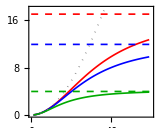

```mathematica
lineslegends={"  Γ_nl = 7×10^13 m^-2 s^-2", "  Γ_nl = 1×10^14 m^-2 s^-2","  Γ_nl = 3×10^14 m^-2 s^-2"};
lineslegends={"","",""};
labeloffset={122,-130};
imagewidth = 160;
font = {9, Black,FontFamily->"CMU Serif"};
t = 0.0075; (* thickness of the lines *)

styles =Append[#, Thickness[t]] &/@{{Full,Red},{Blue},{Darker[Green]},{Dotted,Gray}};
stylesFlat=Append[#, Thickness[t]] &/@ {{Dashed,Red},{Dashed,Blue},{Dashed,Darker[Green]}};
p1=Show[ListPlot[data,Frame->True,Joined->True,ImageSize->imagewidth, AspectRatio->0.8,LabelStyle->font,FrameLabel->{MaTeX@"X_S \,{\\rm [ nm]}", "SNR"},PlotRange->{{All,60},{All,18.0}},PlotStyle->styles,FrameStyle->Directive[Black,Thickness[t]]],

Plot[{AsymptoteColl[7*10^13],AsymptoteColl[1*10^14],AsymptoteColl[3*10^14]},{x,0,100},PlotStyle->stylesFlat,LabelStyle->{13,Black}, PlotLabels->Placed[lineslegends,{Below,Below,Below}]]]
```

#### plot the same against Q_damped

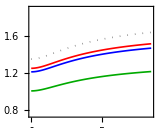

```mathematica
qdata={Import[StringJoin[root,"data/Qd, Gamma_nl=7.00e+13, t=240s.dat"]],
Import[StringJoin[root,"data/Qd, Gamma_nl=1.00e+14, t=240s.dat"]],
Import[StringJoin[root,"data/Qd, Gamma_nl=3.00e+14, t=240s.dat"]],
Import[StringJoin[root,"data/Qd, Gamma_nl=1.00e+00, t=240s.dat"]]};
qdata= ToExpression[#]&/@qdata;

p2=Show[ListPlot[qdata,Frame->True,Joined->True,ImageSize->imagewidth,LabelStyle->font,FrameLabel->{MaTeX@"10^{-5}\, Q_{\\rm fd}", "SNR"},PlotRange->{{0,8.5},{0.75,1.9}},AspectRatio->0.8,PlotStyle->styles,FrameStyle->Directive[Black,Thickness[t]], FrameTicks->{{Automatic,None},{Automatic,Automatic}}]]
```

```mathematica
grid = GraphicsGrid[{{p1, p2}}];
Export[filepath["snrplot.svg"],%]
```

/home/hrochan/polybox/thesis/data/spins/snrplot.svg

#### noise component breakdown

```mathematica
(* force PSD data *)
PSDsForce=Import[StringJoin[root,"data/PSDs_force_Gamma_nl=1.00e+14.dat"]];
PSDsForce= ToExpression[#]&/@PSDsForce;

(* scale the y-axis *)
Fscale=10^6; 
PSDsForce = {#[[1]],Fscale#[[2]],Fscale#[[3]],Fscale#[[4]],Fscale#[[5]],Fscale#[[6]]}&/@PSDsForce;

(* displacement PSD data *)
PSDsDisp=Import[StringJoin[root,"data/PSDs_disp_Gamma_nl=1.00e+14.dat"]];
PSDsDisp= ToExpression[#]&/@PSDsDisp;
```

```mathematica
(* pick the nice colors *)

style = {Thickness[t],#,LineColor->Black}&/@ (ColorData[97,"ColorList"][[{1,3,2,5,4}]]);
Xlabel = MaTeX@"\\frac{\\omega - \\omega_A}{2\\pi} \, {\\rm [s\\textsuperscript{-1}]}";
labeloffset={66,-149};
imagesize = 150;
aspect = 1;

(* forces, lin-lin *)
PSD1=ListPlot[{{#[[1]],#[[6]]}&/@PSDsForce,
{#[[1]],#[[5]]}&/@PSDsForce,
{#[[1]],#[[4]]}&/@PSDsForce,
{#[[1]],#[[3]]}&/@PSDsForce,
{#[[1]],#[[2]]}&/@PSDsForce},
Joined->True, LabelStyle->font, Frame->True,FrameLabel->{Xlabel,"force PSD [aN^2s]"},ImageSize->imagesize,GridLines->None,Axes->None,Filling->{5->Axis, 4->{5},3->{4},2->{3},1->{2} },FillingStyle->Opacity[0.8],AspectRatio->aspect,
PlotStyle->style,PlotRangePadding->{None,Automatic},PlotRange->{Automatic,{0,Automatic}},FrameStyle->Directive[Black,Thickness[t]],Epilog->Style[Text["(a)", Center, Offset[labeloffset]], font]]



(* displacements, lin-lin *)
ticks=Table[If[Mod[i,0.5]==0.,{i,NumberForm[i,{2,1}]},{i,"",{0.005,0.0}}],{i,0,2,0.1}]; (* PSD2 y-axis *)

PSD2=ListPlot[{{#[[1]],#[[6]]}&/@PSDsDisp,
{#[[1]],#[[5]]}&/@PSDsDisp,
{#[[1]],#[[4]]}&/@PSDsDisp,
{#[[1]],#[[3]]}&/@PSDsDisp,
{#[[1]],#[[2]]}&/@PSDsDisp},
Joined->True, LabelStyle->font, Frame->True, FrameLabel->{Xlabel,"displacement PSD [fm^2s]"},ImageSize->imagesize,GridLines->None,Axes->None,Filling->{5->Axis, 4->{5},3->{4},2->{3},1->{2} },FillingStyle->Opacity[0.8],AspectRatio->aspect,
PlotStyle->style,FrameTicks->{{ticks,None},{Automatic,None}},
PlotRangePadding->{None,Automatic},PlotRange->{Automatic,{0,Automatic}},FrameStyle->Directive[Black,Thickness[t]], Epilog->Style[Text["(b)", Center, Offset[labeloffset]], font]]

GraphicsGrid[{{PSD1, PSD2}}]
Export[filepath["PSDs.svg"],%];


(* plots for when only thermal / displacement noise + signal are visible *)
(*(* forces, lin-lin, leaving out small components *)
ListPlot[{{#[[1]],#[[6]]}&/@PSDsForce,
{#[[1]],#[[5]]}&/@PSDsForce,
{#[[1]],#[[4]]}&/@PSDsForce},
Joined->True, LabelStyle->font, Frame->True,FrameLabel->{Xlabel,"force PSD (aN^2s)"},ImageSize->450,GridLines->None,Axes->None,Filling->{3->Axis,2->{3},1->{2} },FillingStyle->Opacity[0.8],
PlotStyle->style,PlotRangePadding->{None,Automatic},PlotRange->{Automatic,{0,Automatic}},FrameStyle->Directive[Black,Thickness[0.004]]]
Export[filepath["PSDs_force_3var.pdf"],%]

(* displacements, lin-lin, leaving out small components *)
ListPlot[{{#[[1]],#[[6]]}&/@PSDsDisp,
{#[[1]],#[[5]]}&/@PSDsDisp,
{#[[1]],#[[4]]}&/@PSDsDisp},
Joined->True, LabelStyle->font, Frame->True, FrameLabel->{StringJoin[Xlabel," (a) (b) (c)"],"displacement PSD  (fm^2s)"},ImageSize->450,GridLines->None,Axes->None,Filling->{3->Axis,2->{3},1->{2} },FillingStyle->Opacity[0.8],
PlotStyle->style,
PlotRangePadding->{None,Automatic},PlotRange->{Automatic,{0,Automatic}},FrameStyle->Directive[Black,Thickness[0.004]]]
Export[filepath["PSDs_disp_3var.pdf"],%]*)
```

-Graphics-

-Graphics-

-Graphics-